## Depict Tiles

```mathematica
TileVertices[step_][or_,dir_,ref_,pt_] := With[{
basicVertices = AnglePath[{
		{step[[2]], -Pi/6+dir*Pi/6},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[2]], -Pi/2},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], -Pi/3},
		{step[[2]], Pi/2},
		{step[[2]], -Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[1]], 0}
	}]
},
	Expand[# + or&/@(If[ref,{-#[[1]],#[[2]]},#]&/@((#-basicVertices[[pt]])&/@basicVertices))]
]
```

```mathematica
TileEdges[step_][or_,dir_,ref_,pt_] := Partition[TileVertices[step][or,dir,ref,pt], 2, 1, 1]
```

```mathematica
Tile[step_][or_,dir_,ref_,pt_] := Polygon[TileVertices[step][or,dir,ref,pt]]
```

```mathematica
hatVertices:=TileVertices[{1, Sqrt[3]}];
hatEdges:=TileEdges[{1, Sqrt[3]}];
hat:=Tile[{1, Sqrt[3]}];
```

```mathematica
spectreVertices:=TileVertices[{1,1}];
spectreEdges:=TileEdges[{1,1}];
spectre:=Tile[{1,1}];
```

```mathematica
canonicalHat[or_,dir_,ref_,pt_]:={hatVertices[or,dir,ref,pt][[1]], dir, ref, 1}
```

## Manipulate Cluster

```mathematica
rotateCluster[tiles_,r_]:=tiles/.p_Polygon:>RotationTransform[r*Pi/6][p]

translateCluster[tiles_,vec_]:=tiles/.p_Polygon:>TranslationTransform[vec][p]

placeCluster[pos_,dir_,tiles_]:=translateCluster[rotateCluster[tiles,dir],pos];
```

```mathematica
rotateTiling[tiling_, r_] := <|
	"tiles" -> rotateCluster[tiling["tiles"], r],
	"controlPoints" -> (Expand[RotationMatrix[r * Pi/6] . #] & /@ tiling["controlPoints"])
|>

translateTiling[tiling_, vec_] := <|
	"tiles" -> translateCluster[tiling["tiles"], vec],
	"controlPoints" -> (Expand[# + vec] & /@ tiling["controlPoints"])
|>

placeTiling[pos_, dir_, code_] := translateTiling[rotateTiling[code, dir], pos];
```

```mathematica
reflectCode[tiles_]:=tiles/.p_Polygon:>ReflectionTransform[{1,0}][p]
reflectTiling[tiling_] := <|"tiles"->reflectCode[tiling["tiles"]],"controlPoints"->Apply[{-#1,#2}&,tiling["controlPoints"],1]|>
```

## Substitution Rule

### spectre rule works for Tile(1,1), (Tile(1,√3)Tile(√3,1)) pair

```mathematica
substitute["spectre"][tiling1_,tiling2_]:=With[
{
t1=reflectTiling[tiling1],
t2=reflectTiling[tiling2]
},
Module[
{
T1,T2,T3,T4,T5,T6,T7,T8,
orgionPoint
},
T1=t2;
T2=placeTiling[
Expand[T1["controlPoints"][[4]]-Dot[RotationMatrix[-2Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-2,t2];

T3=placeTiling[
T2["controlPoints"][[3]],
-2,t2];

T4=placeTiling[
Expand[T3["controlPoints"][[4]]-Dot[RotationMatrix[-4Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-4,t2];

T5=placeTiling[
Expand[T4["controlPoints"][[4]]-Dot[RotationMatrix[-6Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-6,t2];

T6=placeTiling[
T5["controlPoints"][[3]],
-6,t2];

T7=placeTiling[
Expand[T6["controlPoints"][[4]]-
Dot[RotationMatrix[-8Pi/6],(t2["controlPoints"][[2]]-t2["controlPoints"][[1]])]],
-8,t2];

T8=placeTiling[
Expand[T7["controlPoints"][[4]]-Dot[RotationMatrix[-4Pi/6],(t1["controlPoints"][[4]]-t1["controlPoints"][[1]])]],
-4,t1
];

With[{newOriginPt=T7["controlPoints"][[3]]},
<|
"tiling1"-><|
"tiles"->translateCluster[Join@@(#["tiles"]&/@{T1,T2,T4,T5,T6,T7,T8}),-newOriginPt],
"controlPoints"->
(#-newOriginPt&/@{T7["controlPoints"][[3]],T6["controlPoints"][[2]],T4["controlPoints"][[3]],T1["controlPoints"][[2]]})
|>,
<|
"tiling2"-><|
"tiles"->translateCluster[Join@@(#["tiles"]&/@{T1,T2,T3,T4,T5,T6,T7,T8}),-newOriginPt],
"controlPoints"->
(#-newOriginPt&/@{T7["controlPoints"][[3]],T6["controlPoints"][[2]],T4["controlPoints"][[3]],T1["controlPoints"][[2]]})
|>
|>
|>
]
]
]
```

### hat rule works for hat only

```mathematica
substitute["hat"][tiling1_,tiling2_]:=With[
{
t1=placeTiling[-tiling1["controlPoints"][[1]],0,tiling1],
t2=placeTiling[-tiling2["controlPoints"][[1]],0,tiling2]
},
Module[
{
T1,T2,T3,T4,T5,T6,T7,T8
},
T1=t2;
T2=placeTiling[T1["controlPoints"][[4]]-RotationMatrix[10Pi/6].t2["controlPoints"][[2]],10,t2];
T3=placeTiling[T2["controlPoints"][[4]]-RotationMatrix[8Pi/6].t2["controlPoints"][[2]],8,t2];
T4=placeTiling[T3["controlPoints"][[3]],8,t2];
T5=placeTiling[T4["controlPoints"][[4]]-RotationMatrix[6Pi/6].t2["controlPoints"][[2]],6,t2];
T6=placeTiling[T5["controlPoints"][[4]]-RotationMatrix[4Pi/6].t2["controlPoints"][[2]],4,t2];
T7=placeTiling[T6["controlPoints"][[4]]-RotationMatrix[8Pi/6].t2["controlPoints"][[4]],8,t1];

Sow[{T1,T2,T3,T4,T5,T6,T7}];

<|
"tiling1"->placeTiling[tiling1["controlPoints"][[1]],0,
<|
"tiles"->Join@@(#["tiles"]&/@{T1,T2,T3,T5,T6,T7}),
"controlPoints"->{
T1["controlPoints"][[2]],
T2["controlPoints"][[3]],
T4["controlPoints"][[2]],
T6["controlPoints"][[3]]
}
|>
],
<|
"tiling2"->placeTiling[tiling1["controlPoints"][[1]],0,
<|
"tiles"->Join@@(#["tiles"]&/@{T1,T2,T3,T4,T5,T6,T7}),
"controlPoints"->{
T1["controlPoints"][[2]],
T2["controlPoints"][[3]],
T4["controlPoints"][[2]],
T6["controlPoints"][[3]]
}
|>
]
|>
|>

]
]
```

## Visualization

```mathematica
Options[depictControlPoints]=Join[Options[Graphics],Options[Show],{step->{1,1},chooseColor->{Blue,Yellow},"controlPoints"->True}];
depictControlPoints[tile_,opt:OptionsPattern[]]:=
Graphics[
{
EdgeForm[Purple],
tile["tiles"],
If[OptionValue["controlPoints"]===True,
{Red,PointSize[.03],
Point[tile["controlPoints"]],
Line[Partition[tile["controlPoints"],2,1,1]]
},
Nothing
]
},
Sequence@@FilterRules[{opt},Options[Graphics]]
];
```

## Tiles Information

### Turtles + Hat

```mathematica
TH1Tiling=
<|
"tiles"->{{Lighter@Blue,Opacity[.4],Tile[{Sqrt[3],1}][{0,0},4,True,6]}},
"controlPoints"->(TileVertices[{Sqrt[3],1}]@@{{0,0},4,True,6})[[{6,4,2,12}]]
|>;
TH2Tiling=
<|"tiles"->{
{Lighter@Blue,Opacity[.7],Tile[{Sqrt[3],1}][{0,0},4,True,6]},
{Green,Tile[{1,Sqrt[3]}][(TileVertices[{Sqrt[3],1}]@@{{0,0},4,True,6})[[2]],3,True,8]}
},
"controlPoints"->(TileVertices[{Sqrt[3],1}]@@{{0,0},4,True,6})[[{6,4,2,12}]]
|>;
```

### Hats + Turtle

```mathematica
HT1Tiling=
<|
"tiles"->{{LightGray,hat[{0,0},4,True,6]}},
"controlPoints"->(hatVertices@@{{0,0},4,True,6})[[{6,4,2,12}]]
|>;
HT2Tiling=
<|"tiles"->{
{LightGray,hat[{0,0},4,True,6]},
{Purple,Tile[{Sqrt[3],1}][(hatVertices@@{{0,0},4,True,6})[[2]],3,True,8]}
},
"controlPoints"->(hatVertices@@{{0,0},4,True,6})[[{6,4,2,12}]]
|>;
```

### Spectre tiles

```mathematica
S1Tiling=<|
"tiles"->{{Lighter@Green,spectre@@{{0,0},4,True,6}}},
"controlPoints"->(spectreVertices@@{{0,0},4,True,6})[[{6,4,2,12}]]
|>;
S2Tiling=<|"tiles"->
{
{Green,spectre@@{{0,0},4,True,6}},
{Darker@Green,spectre@@{{-√3,√3},3,True,8}}
},
"controlPoints"->(spectreVertices@@{{0,0},4,True,6})[[{6,4,2,12}]]
|>;
```

### Hats only

#### H1 and H2

```mathematica
H1Tiling=<|
"tiles"->{{LightBlue,Opacity[.8],EdgeForm[Black],Tile[{1,Sqrt[3]}]@@{{0,0},8,False,6}}},
"controlPoints"->(TileVertices[{1,Sqrt[3]}]@@{{0,0},8,False,6})[[{6,4,2,12}]]
|>;
H2Tiling=<|"tiles"->
{
{Lighter@Blue,Opacity[.7],EdgeForm[Black],Tile[{1,Sqrt[3]}]@@{{0,0},8,False,6}},
{Darker@Blue,Opacity[.8],EdgeForm[Black],Tile[{1,Sqrt[3]}]@@{(TileVertices[{1,Sqrt[3]}]@@{{0,0},8,False,6})[[1]],2,True,9}}
},
"controlPoints"->(TileVertices[{1,Sqrt[3]}]@@{{0,0},8,False,6})[[{6,4,2,12}]]
|>;
```

#### H7 and H8

```mathematica
H7Tiling=<|"tiles"->{
{Red,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Red,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Red,Opacity[0.9],EdgeForm[Black],Polygon[…]},{Yellow,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Lighter@Blue,Opacity[0.7],EdgeForm[Black],Polygon[…]},
{Lighter@Blue,Opacity[0.7],EdgeForm[Black],Polygon[…]},
{Darker@Blue,Opacity[1],EdgeForm[Black],Polygon[…]}
},"controlPoints"->{{-2,0},{0,4 √3},{7,5 √3},{9,-√3}}|>;;
```

```mathematica
H8Tiling=<|"tiles"->{
{Red,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Red,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Red,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Red,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Yellow,Opacity[0.8],EdgeForm[Black],Polygon[…]},{Lighter@Blue,Opacity[0.7],EdgeForm[Black],Polygon[…]},
{Lighter@Blue,Opacity[0.7],EdgeForm[Black],Polygon[…]},
{Darker@Blue,Opacity[1],EdgeForm[Black],Polygon[…]}
},"controlPoints"->{{-2,0},{0,4 √3},{7,5 √3},{9,-√3}}|>;
```

## Different Color Rule

### only hats

```mathematica
res=NestList[Values[substitute["hat"][#[[1]],#[[2]]]]&,{H7Tiling,H8Tiling},2];
```

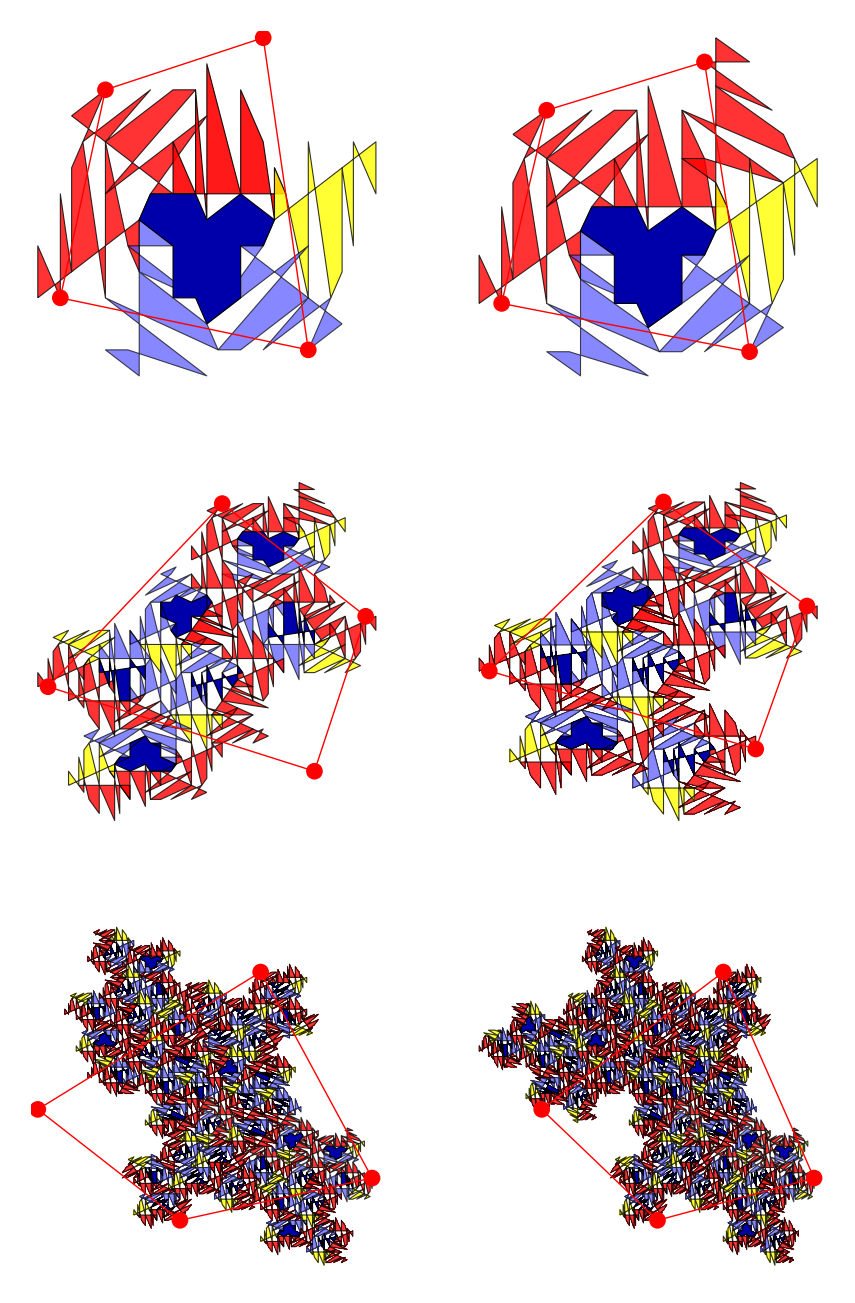

```mathematica
Map[depictControlPoints,res,{2}]//GraphicsGrid
```

It is strange that one of the control points is not on the boundary.

## Try What Author does

### hats

```mathematica
res=NestList[Values[substitute["hat"][#[[1]],#[[2]]]]&,{H2Tiling,H1Tiling},3];
```

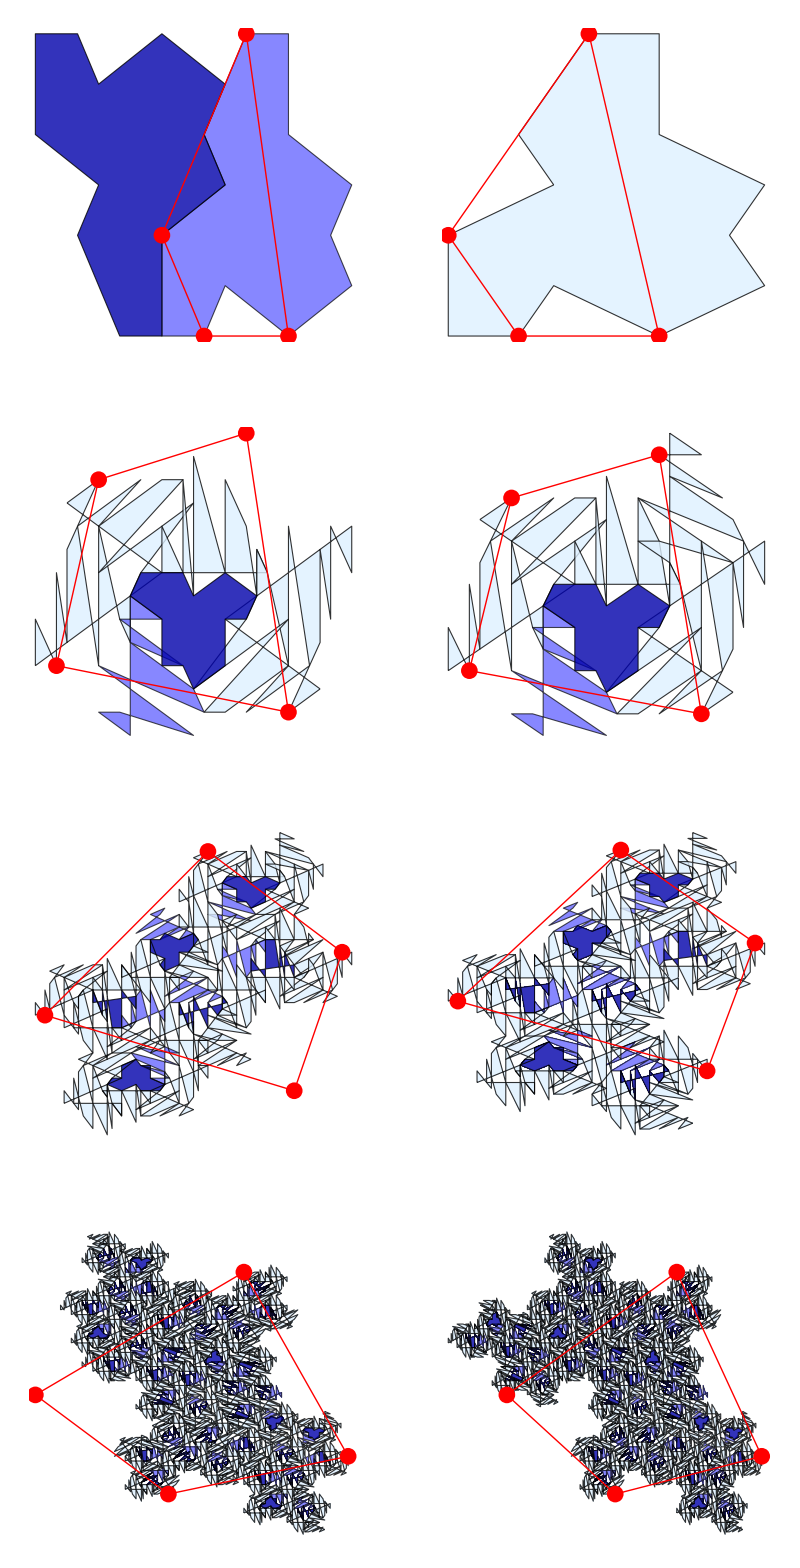

```mathematica
Map[depictControlPoints,res,{2}]//GraphicsGrid
```

### turtles + hat

```mathematica
res=NestList[Values[substitute["spectre"][#[[1]],#[[2]]]]&,{TH2Tiling,TH1Tiling},3];
```

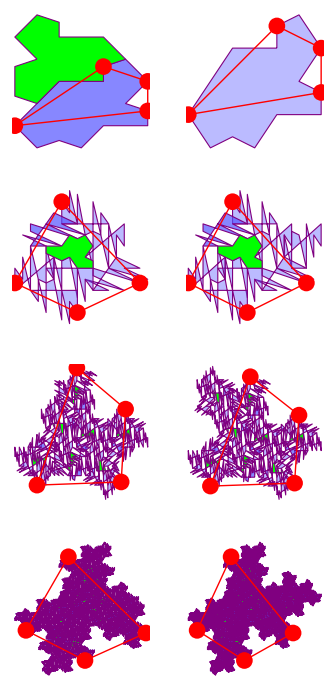

```mathematica
GraphicsGrid[Map[depictControlPoints,res,{2}]]
```

### hats + turtle

```mathematica
res=NestList[Values[substitute["spectre"][#[[1]],#[[2]]]]&,{HT2Tiling,HT1Tiling},3];
```

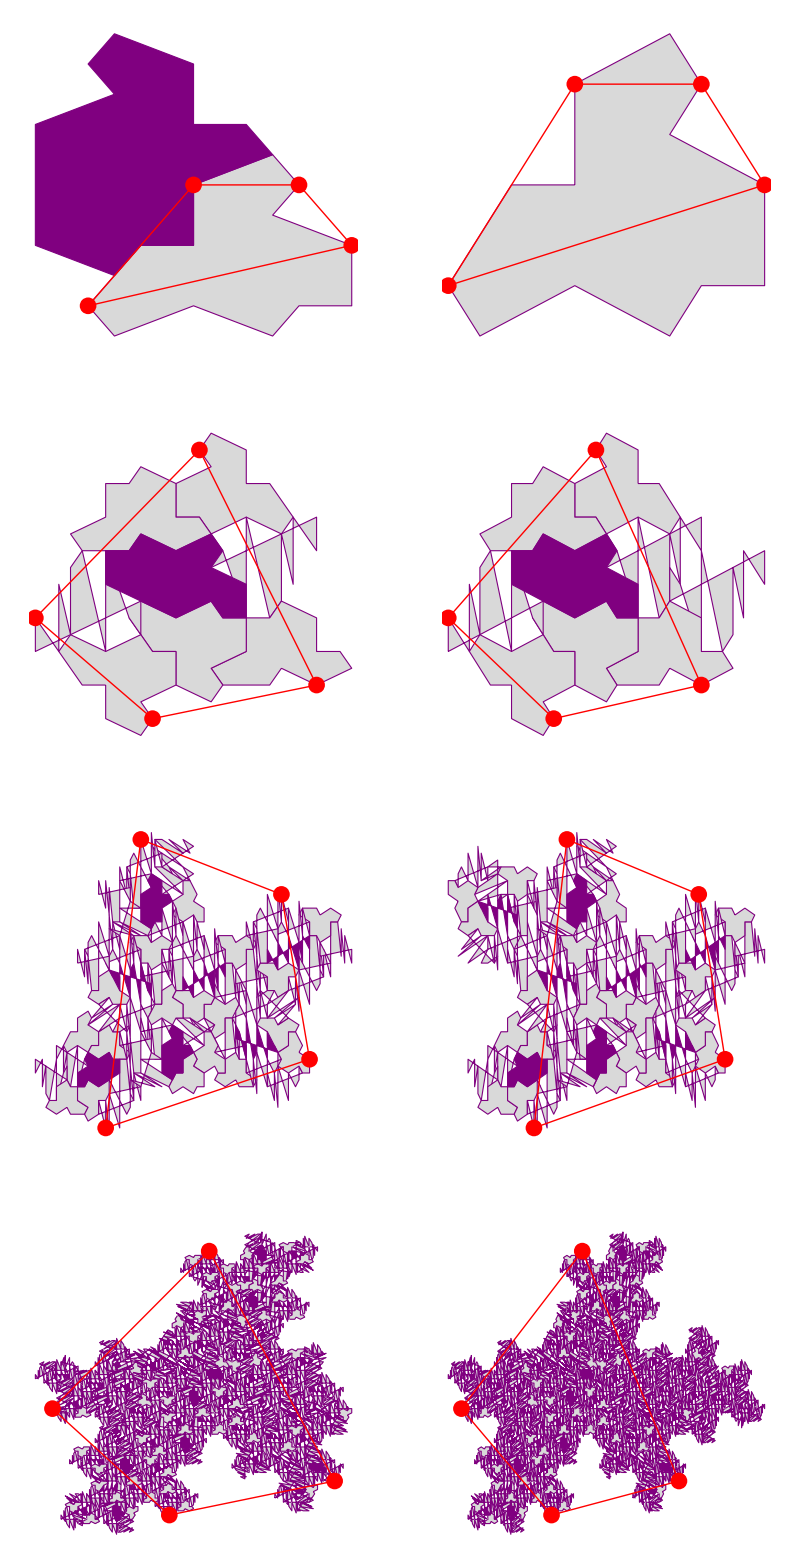

```mathematica
GraphicsGrid[Map[depictControlPoints,res,{2}]]
```

### spectres

```mathematica
res=NestList[Values[substitute["spectre"][#[[1]],#[[2]]]]&,{S2Tiling,S1Tiling},2];
```

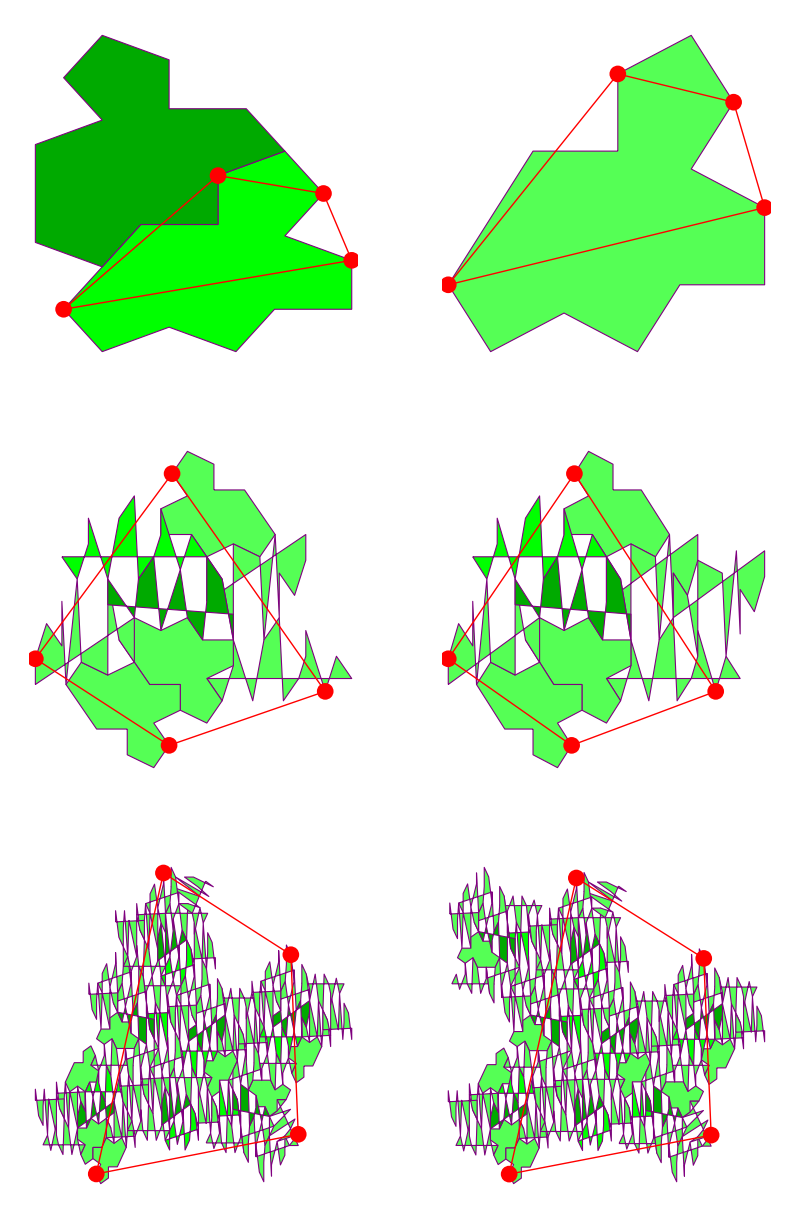

```mathematica
GraphicsGrid[Map[depictControlPoints,res,{2}]]
```

## Create Background

```mathematica
res=NestList[Values[substitute["hat"][#[[1]],#[[2]]]]&,{H2Tiling,H1Tiling},5];
```

```mathematica
range=Mean/@Transpose[Cases[res[[5,2]],p_Polygon:>First[First[p]],All]];
```

```mathematica
range//N
```

{89.3839,48.0282}

```mathematica
Export[NotebookDirectory[]<>"img.png",
depictControlPoints[res[[6,2]]/.{LightBlue->Darker@Blue,Darker@Blue->Black,Lighter@Blue->Darker@Gray},
"controlPoints"->False,
PlotRange->({N@#-100,N@#}&/@range),
ImageSize->3000
]
]
```

C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\FractalSubstitutionRule\img.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\hp\\Desktop\\Wolfram Summer School\\project\\Tile\\FractalSubstitutionRule\\img.png"]]]
```